# Galáxia NGC 1090

## Tabelas

```mathematica
data = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\data_new\\1090.dat"];
RC=Table[{data[[i,1]],data[[i,3]]},{i,1,24}];
Rgas=Table[{data[[i,1]],data[[i,4]]},{i,1,24}];

Erro = Table[data[[i,5]],{i,1,24}];
radii=Part[Transpose[data],1];
Vel=Part[Transpose[data],3];
err=Part[Transpose[data],5];
TableForm[data,TableHeadings->{{"NGC 1090"},{"Raio","","Vtotal","Vgas","Erro"}}]
```

| Raio |  | Vtotal | Vgas | Erro
NGC 1090 | 0.347368 | 3.4723 | 20.88 | -0.813067 | 9.81
 | 1.04211 | 3.50686 | 61.73 | -2.48381 | 8.19
 | 1.56316 | 3.57333 | 81.26 | -3.69901 | 4.32
 | 3.62105 | 4.04191 | 124.02 | -7.34289 | 3.41
 | 4.98246 | 4.42132 | 156.15 | -9.31053 | 7.02
 | 6.46667 | 5.10939 | 166.47 | -10.7933 | 6.34
 | 7.98947 | 6.01784 | 165.26 | -5.73686 | 12.05
 | 8.91228 | 6.38245 | 173.99 | 9.56049 | 4.84
 | 10.1018 | 6.58873 | 164.38 | 17.7079 | 5.86
 | 10.9965 | 6.53136 | 175.97 | 22.4891 | 7.35
 | 13.3193 | 5.92514 | 174.02 | 31.6324 | 3.28
 | 14.7368 | 5.41066 | 167.69 | 35.2506 | 2.23
 | 15.9649 | 4.92757 | 166.39 | 37.8353 | 2.23
 | 17.193 | 4.49278 | 167.05 | 39.7589 | 4.59
 | 18.4211 | 4.058 | 166.57 | 41.3701 | 5.3
 | 19.6491 | 3.67152 | 165.26 | 42.479 | 3.48
 | 20.8772 | 3.33335 | 164.83 | 43.2492 | 3.12
 | 22.1053 | 3.09181 | 164.98 | 43.7767 | 2.39
 | 23.3333 | 2.94688 | 164.6 | 44.6902 | 2.23
 | 24.5614 | 2.75364 | 162.77 | 46.2975 | 2.23
 | 25.7895 | 2.51209 | 162.08 | 47.9662 | 2.23
 | 27.0175 | 2.22224 | 162.23 | 49.6384 | 2.23
 | 28.2456 | 1.83576 | 161.54 | 51.024 | 2.23
 | 29.4737 | 1.34984 | 160.18 | 52.0913 | 2.23

## Interpolação

```mathematica
Igas = Interpolation[Rgas]
```

InterpolatingFunction[{{0.347368, 29.4737}}, <>]

InterpolatingFunction::dmval: Input value {0.279901} lies outside the range of data in the interpolating function. Extrapolation will be used.

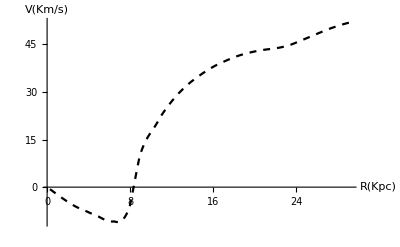

```mathematica
Gas =Plot[Igas[x],{x,0.27931,29.2},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Km/s)"}]
```

## Definindo Equações

```mathematica
Vd[r_,M_]:=1/(2 Rd)(G (M *10^9) (r/Rd)^2) (BesselI[0,r/(2 Rd)] BesselK[0,r/(2 Rd)]-BesselI[1,r/(2 Rd)] BesselK[1,r/(2 Rd)]);
Vme[r_,R_,P_]:=(6.4 G ((P *10^7) R^3) (1/2 Log[(r/R)^2+1]+Log[r/R+1]-ArcTan[r/R]))/r;
G:=4.302/10^6;
Rd:=3.4;
Vt[r_,M_,R_,P_]:=Sqrt[Vd[r,M]+Vme[r,R,P]+Igas[r]^2]
```

## Ajuste

```mathematica
Ajuste= NonlinearModelFit[RC,Vt[r,M,R,P],{{R,1,50},{P,1,10},{M,1,50}},r,Weights->1/Erro^2]
```

FittedModel[√(«1»)]

```mathematica
Ajuste["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
R | 9.02996 | 1.11091 | 8.1284 | 6.37386×10^-8
P | 1.78215 | 0.465093 | 3.83182 | 0.00097056
M | 37.0069 | 2.85954 | 12.9416 | 1.78601×10^-11

InterpolatingFunction::dmval: Input value {0.000608771} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

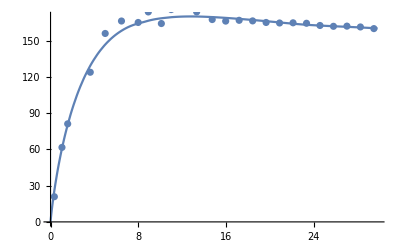

```mathematica
a=Plot[Ajuste[x],{x,0,29.8},AxesOrigin->{0,0}];
Show[a,ListPlot[RC]]
```

## Gráficos

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
RCtotal = Plot[Ajuste[r],{r,0,29.4}, PlotStyle->Black, PlotRange->{{0,30},{0,170}}];Vstars = Plot[Sqrt[Vd[r,M]]/.M->36.5,{r,0,29.4}, PlotStyle->{Black,Dotted}];
Vhalo = Plot[Sqrt[Vme[r,R,P]]/.{R->7.8,P->2.3},{r,0,29.4},PlotStyle->{Black,DotDashed}];
VRC = ErrorListPlot[{Table[{RC[[i]],ErrorBar[Erro[[i]]]},{i,24}]},PlotStyle->Directive[PointSize[0.02],Black]];
Teste = Plot[Vt[r,M,R,P]/.{M->36.5,R->7.8,P->2.3},{r,0,29.4},PlotStyle->Black,PlotRange->{{0,30},{0,190}}];
```

InterpolatingFunction::dmval: Input value {0.0006006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0006006} lies outside the range of data in the interpolating function. Extrapolation will be used.

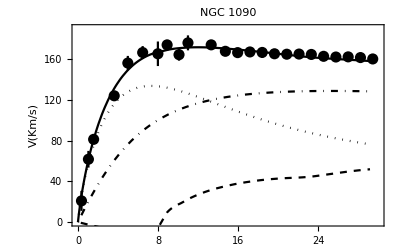

Part::partw: Part 25 of {{0.347368,3.4723,20.88,-0.813067,9.81},{1.04211,3.50686,61.73,-2.48381,8.19},{1.56316,3.57333,81.26,-3.69901,4.32},{3.62105,4.04191,124.02,-7.34289,3.41},{4.98246,4.42132,156.15,-9.31053,7.02},{6.46667,5.10939,166.47,-10.7933,6.34},«12»,{23.3333,2.94688,164.6,44.6902,2.23},{24.5614,2.75364,162.77,46.2975,2.23},{25.7895,2.51209,162.08,47.9662,2.23},{27.0175,2.22224,162.23,49.6384,2.23},{28.2456,1.83576,161.54,51.024,2.23},{29.4737,1.34984,160.18,52.0913,2.23}} does not exist.

Part::partw: Part 25 of {-5.07519,0.859221,0.744923,-5.39494,9.20152,8.09184,0.817484,7.28296,-4.35356,6.34905,3.81722,-2.03259,-2.67971,-1.18178,-0.756758,-1.07031,-0.461927,0.739666,1.25381,0.0657027,-0.0667056,0.575877,0.409605,-0.373143} does not exist.

Part::partw: Part 26 of {{0.347368,3.4723,20.88,-0.813067,9.81},{1.04211,3.50686,61.73,-2.48381,8.19},{1.56316,3.57333,81.26,-3.69901,4.32},{3.62105,4.04191,124.02,-7.34289,3.41},{4.98246,4.42132,156.15,-9.31053,7.02},{6.46667,5.10939,166.47,-10.7933,6.34},«12»,{23.3333,2.94688,164.6,44.6902,2.23},{24.5614,2.75364,162.77,46.2975,2.23},{25.7895,2.51209,162.08,47.9662,2.23},{27.0175,2.22224,162.23,49.6384,2.23},{28.2456,1.83576,161.54,51.024,2.23},{29.4737,1.34984,160.18,52.0913,2.23}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

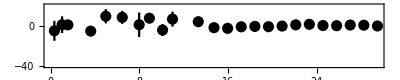

```mathematica
Show[Teste,VRC,Vstars,Vhalo,Gas, Frame->True,PlotRange->{{0,30},{0,190}},PlotLabel->Style["NGC 1090",Black],FrameStyle->Black,FrameLabel->{"","V(Km/s)"}]
ErrorListPlot[{Table[{Table[{data[[i,1]],Ajuste["FitResiduals"][[i]]},{i,26}][[i]],ErrorBar[Erro[[i]]]},{i,24}]}, PlotStyle->Directive[PointSize[0.02],Black],FrameStyle->Black,FrameLabel->{"R (Kpc)",""}, PlotRange->{-40,20},Frame->True, AspectRatio->0.2]
```

```mathematica
chi2[M_,R_,P_]:=N[Plus@@Table[(Vel[[i]]-Vt[radii[[i]],M,P,R])^2/(err[[i]])^2,{i,Dimensions[radii][[1]]}]]
```

```mathematica
BestFit = Timing[NMinimize[{chi2[M,P,R],M>1&&M<50&&P>1 && P<10 && R>1 && R<10},{M,P,R}]]
```

{1.6875,{14.0999,{M→37.0069,P→1.78215,R→9.02996}}}

```mathematica
14.1/21
```

0.671429